{{p[x]→InterpolatingFunction[…][x]}}

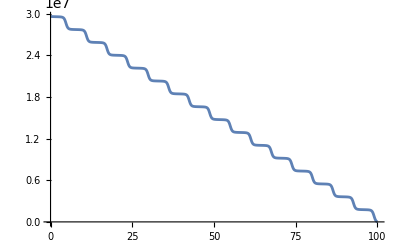

```mathematica
b=1;
l=100;
a=(0.9-b)/l;
μ=1000;
w[x_]:=(a x+b);
w[x_]:=0.4*Sin[x/1]+0.6
q=1;
m=NDSolve[{-w[x]^3/(12 μ)*p'[x]==q,p[l]==0},p[x],{x,0,l}]
Plot[p[x]/.m,{x,0,l}]
```

```mathematica
m[[1]]
```

{p[x]→-5.35908×10^17-3.4117×10^17 ArcTan[45.297 (-3999.99+2. x)]+1.96974×10^17 Log[2000.01-1. x]-9.84868×10^16 Log[3.99997×10^6-3999.99 x+1. x^2]}

```mathematica
ϕm=0.9;
ϕM=0.1;
phi[y_]:=(ϕM ϕm)/((1-y^2)ϕm + y^2 ϕM);
mu[ϕ_]:=1/(1-ϕ)^2.5;
u[y_]:=NIntegrate[ξ/mu[phi[ξ]],{ξ,y,1}];
Plot[phi[y],{y,0,1},PlotLabels->"Expressions",PlotRange->Full]
Plot[mu[phi[y]],{y,0,1},PlotLabels->"Expressions",PlotRange->Full]
Plot[u[y],{y,0,1},PlotLabels->"Expressions",PlotRange->Full]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
NIntegrate[ξ/mu[phi[ξ]],ξ]
```

3.44355 (0.12+ξ^2)^(7/2) Hypergeometric2F1[2.5,3.5,4.5,-0.428571-3.57143 ξ^2]